```mathematica
A=-4.55;
B=11495;
c=342-273.15;
mu[T_]:=Exp[A+B/(T-c)];
```

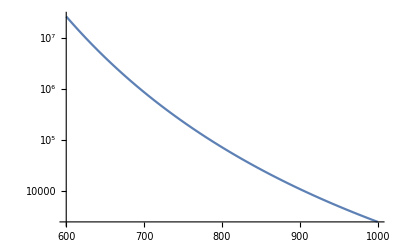

```mathematica
LogPlot[mu[T],{T,600, 1000}]
```

```mathematica
ny = 30;
L=5.0;
YB = Table[i,{i,0.0, 1.0, 1.0/ny}]
yb=Table[L*(1-Cos[y*π/2]),{y,YB}]
dy=yb[[2;;-1]]-yb[[1;;-2]]
```

{0.,0.0333333,0.0666667,0.1,0.133333,0.166667,0.2,0.233333,0.266667,0.3,0.333333,0.366667,0.4,0.433333,0.466667,0.5,0.533333,0.566667,0.6,0.633333,0.666667,0.7,0.733333,0.766667,0.8,0.833333,0.866667,0.9,0.933333,0.966667,1.}

{0.,0.00685233,0.0273905,0.0615583,0.109262,0.170371,0.244717,0.332098,0.432273,0.544967,0.669873,0.806647,0.954915,1.11427,1.28428,1.46447,1.65435,1.8534,2.06107,2.2768,2.5,2.73005,2.96632,3.20816,3.45492,3.7059,3.96044,4.21783,4.47736,4.73832,5.}

{0.00685233,0.0205382,0.0341678,0.0477037,0.0611089,0.0743465,0.0873804,0.100175,0.112695,0.124906,0.136774,0.148268,0.159355,0.170006,0.18019,0.189881,0.199051,0.207676,0.215731,0.223195,0.230048,0.236269,0.241843,0.246755,0.25099,0.254537,0.257386,0.25953,0.260963,0.26168}